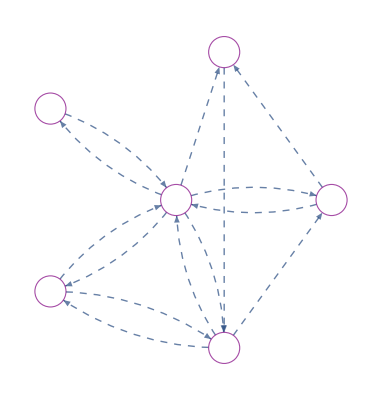

```mathematica
e={"Minsk"->"Grodno","Grodno"->"Minsk","Minsk"->"Gomel","Gomel"->"Minsk","Mogilev"->"Minsk","Minsk"->"Mogilev","Minsk"->"Brest","Brest"->"Minsk","Minsk"->"Vitebsk","Brest"->"Gomel","Gomel"->"Brest","Vitebsk"->"Gomel","Gomel"->"Mogilev","Mogilev"->"Vitebsk"};
g=Graph[e,EdgeWeight->{280,281,311,312,198,199,344,345,292,527,528,331,175,162},VertexLabels->Table[With[{j=VertexList[%][[i]]},j->Placed[{j|Cases[IncidenceList[%,j], j->a_->a]},Tooltip]], {i,VertexCount[%]}],
EdgeLabels->Table[With[{j=EdgeList[%][[i]]},j->Placed[j|PropertyValue[{g,j},EdgeWeight],Tooltip]],{i,EdgeCount[%]}],
GraphLayout->"BalloonEmbedding",VertexSize->Medium,VertexStyle->White,EdgeStyle->Dashed,  BaseStyle->Directive[EdgeForm[Purple], EdgeForm[Thick]]]
```